```mathematica
alldata=Import[FileNameJoin[{NotebookDirectory[],"fixtures","output.csv"}]];
```

```mathematica
dataset=Import[FileNameJoin[{NotebookDirectory[],"fixtures","dataset.csv"}]];
```

```mathematica
data1415=Select[alldata,DateValue[First[#],"Year"]==DateValue[{2014},"Year"]||DateValue[First[#],"Year"]==DateValue[{2015},"Year"]&];
```

```mathematica
holidays=DayRange[DateObject[{2014,1,1}],DateObject[{2015,12,31}],"Holiday",HolidayCalendar->{"UnitedStates", "Default"}];
```

```mathematica
extractDataByYear[l_List,y_Integer]:=Select[l,DateValue[First[#],"Year"]==DateValue[{y},"Year"]&]
```

```mathematica
extractDataByWeekday[l_List,w_Symbol]:=
Select[l,DayName[First[#]]==w&]
```

```mathematica
extractHourlyData[l_List]:=Map[Rest,l]
```

```mathematica
plotListWithModel[l_List,nlm_FittedModel]:=Show[Map[ListPlot,l],Plot[nlm[x],{x,0,24}],PlotRange->All,Ticks->{Range[24],Automatic}]
```

```mathematica
getSampleData[l_List,y_Integer,w_Symbol,n_Integer]:=extractHourlyData[extractDataByWeekday[extractDataByYear[dataset,y],w]][[n]]
```

```mathematica
minMaxMeanPlot[y_Integer,w_Symbol]:=ListLinePlot[{Map[Min,Transpose[Map[Rest,extractDataByWeekday[extractDataByYear[dataset,y],w]]]],Map[Max,Transpose[Map[Rest,extractDataByWeekday[extractDataByYear[dataset,y],w]]]],Map[Mean,Transpose[Map[Rest,extractDataByWeekday[extractDataByYear[dataset,y],w]]]]},PlotRange->All,Filling->{1->{2}},Ticks->{Range[1,24],Automatic},GridLines->{Range[1,24],Automatic}]
```

```mathematica
selectNormalWeekdays[w_Symbol]:=Select[Select[data1415,DayName[First[#]]==w&],FreeQ[holidays,DateObject[DateList[First[#]][[1;;3]]]]&]
```

```mathematica
predictDay[w_Symbol]:=Predict[DateValue[#1,"Hour"]->#2&@@@selectNormalWeekdays[w],Method->"RandomForest"]/@Range[0,23]
```

```mathematica
nlm=NonlinearModelFit[getSampleData[dataset,2015,Monday,24],a+b x+c x^2+d x^3+e x^4,{a,b,c,d,e},x]
```

FittedModel[1110.41-1073.15 x+255.375 x^2-16.7501 x^3+0.329474 x^4]

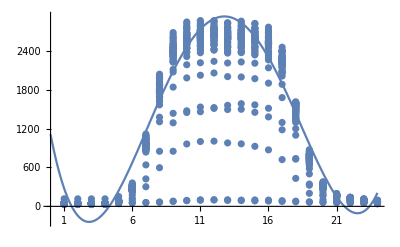

```mathematica
plotListWithModel[extractHourlyData[extractDataByWeekday[extractDataByYear[dataset,2015],Monday]],nlm]
```

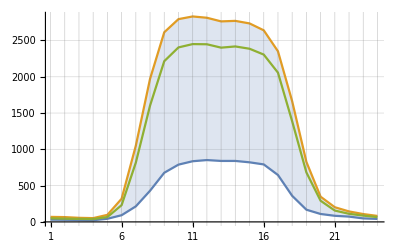

```mathematica
minMaxMeanPlot[2014,Tuesday]
```

```mathematica
(*Extract all data in mondays which max numbers of parking cars is greater than 2000*)
```

```mathematica
selectedMondays=DateObject[DateList[First[#]][[1;;3]]]&/@Select[extractDataByWeekday[dataset,Monday],Max[Rest[#]]>2000&];
```

```mathematica
trainingdataBiased=DateValue[#1,"Hour"]->#2&@@@Select[alldata,MemberQ[selectedMondays,DateObject[DateList[First[#]][[1;;3]]]]&];
```

```mathematica
pBiased=Predict[trainingdataBiased]
```

PredictorFunction[…]

```mathematica
(*Extract all data in mondays*)
trainingdataUnbiased={DateValue[#1,"Hour"],MemberQ[holidays,DateObject[DateList[#1][[1;;3]]]]}->#2&@@@Select[alldata,(DateValue[First[#],"Year"]==DateValue[{2014},"Year"]|| DateValue[First[#],"Year"]==DateValue[{2015},"Year"])&&DayName[First[#]]==Monday&];
```

```mathematica
pUnbiased=Predict[trainingdataUnbiased,Method->"RandomForest"]
```

PredictorFunction[…]

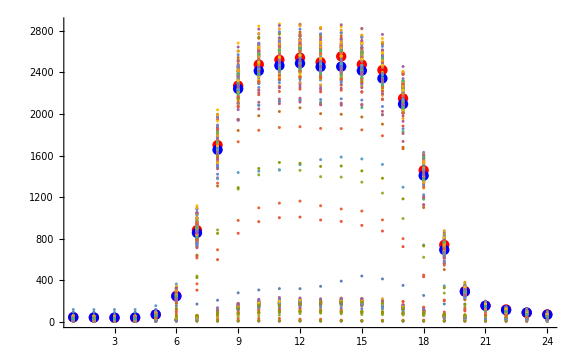

```mathematica
Show[ListPlot[Map[pBiased,Range[0,23]],PlotStyle->Red],ListPlot[Map[pUnbiased,{#,False}&/@Range[0,23]],PlotStyle->Blue],ListPlot[Map[Rest,extractDataByWeekday[dataset,Monday]]],PlotRange->All]
```

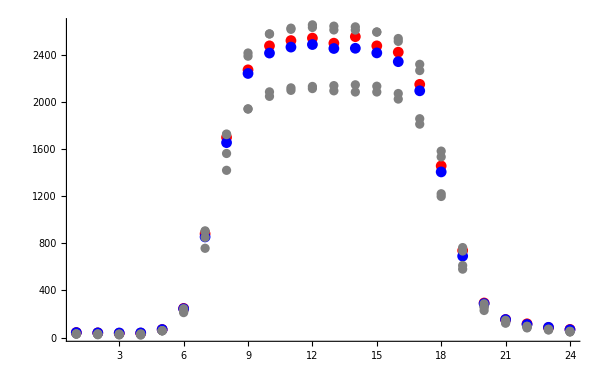

```mathematica
Show[ListPlot[Map[pBiased,Range[0,23]],PlotStyle->Red],ListPlot[Map[pUnbiased,{#,False}&/@Range[0,23]],PlotStyle->Blue],ListPlot[Map[Rest,extractDataByWeekday[extractDataByYear[dataset,2016],Monday]],PlotStyle->Gray],PlotRange->All]
```

```mathematica
(*According to above analysis, Off-Peak Period is (0-4)and(22-23)*)
```

```mathematica
(*From previous view, We can learn from that Peak period the absolute error is great but relative error is small. But in off-peak period relative error is high but absolute error is small.*)
```

```mathematica
DatePlus[#,1]&/@holidays
```

```mathematica
Select[dataset,MemberQ[holidays,DateObject[DateList[First[#]][[1;;3]]]]&]//TableForm
```

2014-01-01 00:00:00 | 11 | 11 | 12 | 10 | 10 | 11 | 12 | 15 | 16 | 19 | 20 | 22 | 23 | 30 | 28 | 27 | 24 | 26 | 19 | 19 | 18 | 20 | 20 | 17
2014-01-20 00:00:00 | 27 | 26 | 24 | 22 | 49 | 198 | 769 | 1533 | 1948 | 2083 | 2123 | 2134 | 2112 | 2094 | 2062 | 1992 | 1830 | 1179 | 562 | 231 | 129 | 92 | 69 | 43
2014-02-17 00:00:00 | 28 | 28 | 28 | 28 | 34 | 76 | 613 | 1334 | 1732 | 1843 | 1870 | 1877 | 1861 | 1859 | 1847 | 1790 | 1665 | 1122 | 543 | 218 | 110 | 74 | 58 | 46
2014-05-26 00:00:00 | 34 | 32 | 30 | 29 | 29 | 29 | 31 | 40 | 48 | 57 | 63 | 77 | 81 | 75 | 68 | 67 | 64 | 62 | 52 | 50 | 48 | 45 | 43 | 44
2014-07-04 00:00:00 | 45 | 40 | 40 | 40 | 40 | 41 | 42 | 49 | 53 | 59 | 61 | 64 | 58 | 60 | 56 | 54 | 52 | 51 | 49 | 50 | 54 | 55 | 53 | 44
2014-09-01 00:00:00 | 45 | 44 | 43 | 45 | 42 | 42 | 45 | 49 | 65 | 79 | 93 | 95 | 102 | 95 | 96 | 89 | 77 | 75 | 68 | 63 | 59 | 56 | 48 | 46
2014-10-13 00:00:00 | 48 | 44 | 41 | 43 | 75 | 260 | 892 | 1670 | 2218 | 2361 | 2399 | 2407 | 2392 | 2399 | 2365 | 2286 | 2041 | 1336 | 663 | 286 | 163 | 124 | 98 | 75
2014-11-11 00:00:00 | 69 | 66 | 56 | 51 | 93 | 301 | 1031 | 1939 | 2475 | 2657 | 2714 | 2677 | 2640 | 2648 | 2621 | 2538 | 2258 | 1442 | 664 | 269 | 163 | 113 | 78 | 61
2014-11-27 00:00:00 | 42 | 40 | 41 | 42 | 42 | 43 | 48 | 60 | 135 | 184 | 183 | 68 | 45 | 44 | 44 | 44 | 42 | 45 | 45 | 43 | 42 | 42 | 43 | 43
2014-12-25 00:00:00 | 42 | 42 | 42 | 44 | 42 | 42 | 42 | 41 | 43 | 43 | 43 | 45 | 42 | 40 | 40 | 39 | 39 | 39 | 41 | 41 | 40 | 40 | 40 | 42
2015-01-01 00:00:00 | 51 | 48 | 47 | 47 | 49 | 50 | 50 | 51 | 50 | 54 | 55 | 53 | 50 | 39 | 40 | 41 | 43 | 44 | 40 | 42 | 40 | 41 | 38 | 38
2015-01-19 00:00:00 | 117 | 116 | 116 | 116 | 153 | 362 | 1045 | 1376 | 1436 | 1449 | 1461 | 1512 | 1560 | 1585 | 1567 | 1514 | 1295 | 738 | 344 | 169 | 105 | 83 | 67 | 49
2015-02-16 00:00:00 | 43 | 43 | 40 | 40 | 76 | 300 | 956 | 1704 | 2075 | 2186 | 2217 | 2239 | 2213 | 2229 | 2210 | 2139 | 1884 | 1199 | 583 | 265 | 149 | 107 | 85 | 67
2015-05-25 00:00:00 | 51 | 51 | 50 | 50 | 52 | 53 | 59 | 65 | 76 | 87 | 94 | 99 | 92 | 89 | 84 | 82 | 76 | 71 | 65 | 62 | 61 | 50 | 51 | 48
2015-07-03 00:00:00 | 54 | 54 | 50 | 47 | 46 | 47 | 55 | 89 | 127 | 145 | 154 | 166 | 160 | 130 | 117 | 105 | 98 | 77 | 68 | 64 | 58 | 60 | 57 | 53
2015-09-07 00:00:00 | 54 | 54 | 54 | 56 | 57 | 56 | 58 | 66 | 80 | 92 | 101 | 102 | 102 | 96 | 99 | 97 | 88 | 80 | 71 | 65 | 59 | 60 | 56 | 54
2015-10-12 00:00:00 | 47 | 43 | 42 | 46 | 75 | 262 | 896 | 1671 | 2226 | 2383 | 2428 | 2432 | 2390 | 2373 | 2353 | 2281 | 2057 | 1372 | 661 | 286 | 151 | 117 | 86 | 67
2015-11-11 00:00:00 | 43 | 37 | 34 | 36 | 78 | 284 | 995 | 1801 | 2310 | 2480 | 2537 | 2544 | 2501 | 2529 | 2493 | 2427 | 2117 | 1427 | 676 | 297 | 174 | 133 | 83 | 59
2015-11-26 00:00:00 | 36 | 38 | 34 | 38 | 35 | 37 | 36 | 34 | 61 | 74 | 76 | 37 | 35 | 34 | 35 | 37 | 36 | 36 | 37 | 36 | 34 | 35 | 35 | 33
2015-12-25 00:00:00 | 31 | 31 | 30 | 34 | 30 | 30 | 31 | 32 | 32 | 31 | 31 | 31 | 32 | 31 | 33 | 33 | 33 | 33 | 33 | 33 | 32 | 32 | 31 | 30

```mathematica
Select[Select[dataset,FreeQ[holidays,DateObject[DateList[First[#]][[1;;3]]]]&],Max[Rest[#]]<2000&&DayName[First[#]]≠Saturday&&DayName[First[#]]≠Sunday&&DayName[First[#]]≠Friday&&(DateValue[First[#],"Year"]==DateValue[{2014},"Year"]||DateValue[First[#],"Year"]==DateValue[{2015},"Year"])&]//TableForm
```

2014-01-02 00:00:00 | 14 | 14 | 13 | 13 | 20 | 99 | 378 | 743 | 1072 | 1196 | 1238 | 1251 | 1249 | 1262 | 1243 | 1167 | 1047 | 679 | 273 | 119 | 69 | 58 | 48 | 27
2014-01-28 00:00:00 | 48 | 41 | 37 | 34 | 43 | 92 | 214 | 429 | 677 | 789 | 836 | 852 | 840 | 840 | 821 | 792 | 662 | 453 | 263 | 142 | 101 | 77 | 61 | 50
2014-07-03 00:00:00 | 54 | 45 | 43 | 45 | 57 | 134 | 468 | 965 | 1390 | 1523 | 1549 | 1539 | 1467 | 1359 | 1242 | 1018 | 688 | 397 | 195 | 131 | 88 | 81 | 64 | 56
2014-08-07 00:00:00 | 54 | 48 | 43 | 45 | 65 | 68 | 89 | 122 | 149 | 163 | 174 | 174 | 168 | 204 | 230 | 230 | 226 | 187 | 129 | 102 | 79 | 74 | 68 | 54
2014-08-25 00:00:00 | 92 | 90 | 87 | 90 | 117 | 153 | 169 | 206 | 277 | 305 | 318 | 317 | 340 | 390 | 439 | 411 | 349 | 252 | 170 | 115 | 93 | 85 | 74 | 55
2014-11-26 00:00:00 | 45 | 41 | 39 | 38 | 52 | 116 | 398 | 757 | 1118 | 1230 | 1265 | 1225 | 1098 | 917 | 694 | 404 | 234 | 173 | 114 | 92 | 84 | 73 | 56 | 42
2014-12-22 00:00:00 | 40 | 40 | 38 | 37 | 47 | 118 | 439 | 883 | 1277 | 1414 | 1461 | 1457 | 1396 | 1392 | 1343 | 1238 | 993 | 620 | 275 | 145 | 92 | 80 | 63 | 48
2014-12-23 00:00:00 | 40 | 40 | 37 | 38 | 54 | 108 | 364 | 751 | 1079 | 1215 | 1242 | 1229 | 1168 | 1096 | 1013 | 880 | 646 | 359 | 168 | 109 | 87 | 73 | 48 | 41
2014-12-24 00:00:00 | 42 | 41 | 40 | 39 | 44 | 67 | 155 | 279 | 399 | 440 | 432 | 413 | 343 | 261 | 181 | 110 | 74 | 69 | 59 | 45 | 40 | 41 | 43 | 44
2014-12-29 00:00:00 | 40 | 40 | 40 | 41 | 51 | 118 | 364 | 692 | 975 | 1096 | 1141 | 1161 | 1116 | 1085 | 1065 | 980 | 799 | 449 | 208 | 128 | 93 | 78 | 68 | 55
2014-12-30 00:00:00 | 46 | 45 | 43 | 43 | 55 | 113 | 366 | 683 | 982 | 1104 | 1124 | 1150 | 1101 | 1067 | 1022 | 932 | 744 | 436 | 209 | 109 | 84 | 75 | 64 | 48
2014-12-31 00:00:00 | 36 | 35 | 35 | 35 | 40 | 82 | 284 | 547 | 779 | 867 | 892 | 902 | 849 | 726 | 572 | 381 | 233 | 132 | 92 | 75 | 67 | 53 | 52 | 51
2015-04-07 00:00:00 | 88 | 89 | 89 | 90 | 106 | 165 | 397 | 659 | 911 | 1019 | 1069 | 1091 | 1157 | 1216 | 1204 | 1145 | 1018 | 705 | 401 | 196 | 128 | 107 | 85 | 69
2015-05-26 00:00:00 | 48 | 46 | 45 | 45 | 55 | 99 | 197 | 318 | 399 | 496 | 572 | 621 | 630 | 634 | 611 | 572 | 504 | 356 | 217 | 142 | 88 | 66 | 58 | 56
2015-06-16 00:00:00 | 69 | 69 | 61 | 57 | 75 | 111 | 289 | 587 | 831 | 916 | 920 | 925 | 908 | 854 | 784 | 668 | 536 | 376 | 230 | 137 | 106 | 81 | 68 | 64
2015-07-02 00:00:00 | 64 | 60 | 57 | 55 | 71 | 178 | 588 | 1198 | 1636 | 1817 | 1860 | 1857 | 1754 | 1651 | 1573 | 1347 | 968 | 573 | 280 | 160 | 117 | 96 | 73 | 59
2015-11-24 00:00:00 | 40 | 35 | 31 | 35 | 49 | 164 | 589 | 1216 | 1701 | 1852 | 1892 | 1894 | 1817 | 1821 | 1771 | 1655 | 1369 | 865 | 383 | 176 | 118 | 88 | 64 | 53
2015-11-25 00:00:00 | 38 | 33 | 31 | 31 | 42 | 89 | 327 | 698 | 1002 | 1133 | 1154 | 1128 | 1043 | 843 | 653 | 398 | 253 | 168 | 121 | 84 | 74 | 56 | 45 | 37
2015-12-21 00:00:00 | 35 | 32 | 31 | 31 | 44 | 127 | 424 | 850 | 1290 | 1475 | 1533 | 1525 | 1495 | 1499 | 1452 | 1381 | 1182 | 729 | 326 | 167 | 111 | 77 | 57 | 42
2015-12-22 00:00:00 | 37 | 34 | 29 | 29 | 39 | 101 | 382 | 805 | 1184 | 1353 | 1399 | 1402 | 1280 | 1282 | 1225 | 1130 | 937 | 563 | 259 | 139 | 88 | 75 | 57 | 48
2015-12-23 00:00:00 | 37 | 36 | 34 | 34 | 41 | 84 | 245 | 511 | 770 | 893 | 915 | 906 | 806 | 686 | 585 | 412 | 266 | 180 | 102 | 77 | 70 | 63 | 48 | 34
2015-12-24 00:00:00 | 32 | 31 | 31 | 31 | 31 | 36 | 64 | 119 | 158 | 181 | 190 | 184 | 142 | 93 | 67 | 50 | 48 | 51 | 40 | 32 | 31 | 30 | 30 | 31
2015-12-28 00:00:00 | 31 | 31 | 31 | 36 | 42 | 96 | 303 | 597 | 851 | 963 | 1001 | 1007 | 979 | 965 | 927 | 872 | 722 | 432 | 201 | 103 | 68 | 59 | 48 | 40
2015-12-29 00:00:00 | 33 | 33 | 29 | 29 | 40 | 93 | 330 | 623 | 890 | 998 | 1037 | 1043 | 1016 | 1000 | 963 | 888 | 729 | 431 | 194 | 104 | 78 | 72 | 55 | 44
2015-12-30 00:00:00 | 36 | 38 | 34 | 35 | 38 | 82 | 277 | 526 | 769 | 877 | 919 | 926 | 895 | 853 | 812 | 720 | 566 | 345 | 158 | 91 | 71 | 64 | 51 | 32
2015-12-31 00:00:00 | 30 | 32 | 35 | 32 | 36 | 57 | 182 | 349 | 490 | 558 | 580 | 579 | 522 | 441 | 340 | 249 | 154 | 96 | 72 | 55 | 48 | 41 | 41 | 43

```mathematica
(*From above analysis, we knwo that some holidays like Washingtong's Day basically has no influence on occupancies. But on the other hand,Christmas has much more influence on occupancies. So we need reconsider how to choose holidays. Deleted Holidays should be #2,#3, #7, #8*)
```

```mathematica
specialDays=Union[Delete[DayRange[DateObject[{2014,1,1}],DateObject[{2015,12,31}],"Holiday",HolidayCalendar->{"UnitedStates","Default"}],List/@{2,3,7,8,12,13,17,18}],{DateObject[{2014,11,26}]},DayRange[DateObject[{2014,12,21}],DateObject[{2014,12,31}]],{DateObject[{2015,11,25}]},DayRange[DateObject[{2015,12,21}],DateObject[{2015,12,31}]]];
```

```mathematica
Select[dataset,MemberQ[specialDays,DateObject[DateList[First[#]][[1;;3]]]]&]//TableForm
```

2014-01-01 00:00:00 | 11 | 11 | 12 | 10 | 10 | 11 | 12 | 15 | 16 | 19 | 20 | 22 | 23 | 30 | 28 | 27 | 24 | 26 | 19 | 19 | 18 | 20 | 20 | 17
2014-05-26 00:00:00 | 34 | 32 | 30 | 29 | 29 | 29 | 31 | 40 | 48 | 57 | 63 | 77 | 81 | 75 | 68 | 67 | 64 | 62 | 52 | 50 | 48 | 45 | 43 | 44
2014-07-04 00:00:00 | 45 | 40 | 40 | 40 | 40 | 41 | 42 | 49 | 53 | 59 | 61 | 64 | 58 | 60 | 56 | 54 | 52 | 51 | 49 | 50 | 54 | 55 | 53 | 44
2014-09-01 00:00:00 | 45 | 44 | 43 | 45 | 42 | 42 | 45 | 49 | 65 | 79 | 93 | 95 | 102 | 95 | 96 | 89 | 77 | 75 | 68 | 63 | 59 | 56 | 48 | 46
2014-11-26 00:00:00 | 45 | 41 | 39 | 38 | 52 | 116 | 398 | 757 | 1118 | 1230 | 1265 | 1225 | 1098 | 917 | 694 | 404 | 234 | 173 | 114 | 92 | 84 | 73 | 56 | 42
2014-11-27 00:00:00 | 42 | 40 | 41 | 42 | 42 | 43 | 48 | 60 | 135 | 184 | 183 | 68 | 45 | 44 | 44 | 44 | 42 | 45 | 45 | 43 | 42 | 42 | 43 | 43
2014-12-21 00:00:00 | 42 | 39 | 39 | 39 | 39 | 38 | 40 | 44 | 59 | 76 | 103 | 102 | 97 | 61 | 70 | 88 | 89 | 77 | 75 | 49 | 45 | 46 | 41 | 39
2014-12-22 00:00:00 | 40 | 40 | 38 | 37 | 47 | 118 | 439 | 883 | 1277 | 1414 | 1461 | 1457 | 1396 | 1392 | 1343 | 1238 | 993 | 620 | 275 | 145 | 92 | 80 | 63 | 48
2014-12-23 00:00:00 | 40 | 40 | 37 | 38 | 54 | 108 | 364 | 751 | 1079 | 1215 | 1242 | 1229 | 1168 | 1096 | 1013 | 880 | 646 | 359 | 168 | 109 | 87 | 73 | 48 | 41
2014-12-24 00:00:00 | 42 | 41 | 40 | 39 | 44 | 67 | 155 | 279 | 399 | 440 | 432 | 413 | 343 | 261 | 181 | 110 | 74 | 69 | 59 | 45 | 40 | 41 | 43 | 44
2014-12-25 00:00:00 | 42 | 42 | 42 | 44 | 42 | 42 | 42 | 41 | 43 | 43 | 43 | 45 | 42 | 40 | 40 | 39 | 39 | 39 | 41 | 41 | 40 | 40 | 40 | 42
2014-12-26 00:00:00 | 41 | 40 | 40 | 40 | 40 | 46 | 75 | 118 | 159 | 175 | 187 | 186 | 180 | 165 | 134 | 103 | 87 | 74 | 59 | 50 | 47 | 46 | 43 | 43
2014-12-27 00:00:00 | 42 | 42 | 44 | 42 | 42 | 42 | 42 | 42 | 46 | 52 | 60 | 61 | 59 | 53 | 44 | 47 | 45 | 41 | 41 | 40 | 41 | 41 | 40 | 42
2014-12-28 00:00:00 | 41 | 40 | 40 | 40 | 40 | 40 | 41 | 42 | 49 | 63 | 80 | 76 | 77 | 54 | 48 | 46 | 44 | 46 | 44 | 41 | 43 | 42 | 41 | 42
2014-12-29 00:00:00 | 40 | 40 | 40 | 41 | 51 | 118 | 364 | 692 | 975 | 1096 | 1141 | 1161 | 1116 | 1085 | 1065 | 980 | 799 | 449 | 208 | 128 | 93 | 78 | 68 | 55
2014-12-30 00:00:00 | 46 | 45 | 43 | 43 | 55 | 113 | 366 | 683 | 982 | 1104 | 1124 | 1150 | 1101 | 1067 | 1022 | 932 | 744 | 436 | 209 | 109 | 84 | 75 | 64 | 48
2014-12-31 00:00:00 | 36 | 35 | 35 | 35 | 40 | 82 | 284 | 547 | 779 | 867 | 892 | 902 | 849 | 726 | 572 | 381 | 233 | 132 | 92 | 75 | 67 | 53 | 52 | 51
2015-01-01 00:00:00 | 51 | 48 | 47 | 47 | 49 | 50 | 50 | 51 | 50 | 54 | 55 | 53 | 50 | 39 | 40 | 41 | 43 | 44 | 40 | 42 | 40 | 41 | 38 | 38
2015-05-25 00:00:00 | 51 | 51 | 50 | 50 | 52 | 53 | 59 | 65 | 76 | 87 | 94 | 99 | 92 | 89 | 84 | 82 | 76 | 71 | 65 | 62 | 61 | 50 | 51 | 48
2015-07-03 00:00:00 | 54 | 54 | 50 | 47 | 46 | 47 | 55 | 89 | 127 | 145 | 154 | 166 | 160 | 130 | 117 | 105 | 98 | 77 | 68 | 64 | 58 | 60 | 57 | 53
2015-09-07 00:00:00 | 54 | 54 | 54 | 56 | 57 | 56 | 58 | 66 | 80 | 92 | 101 | 102 | 102 | 96 | 99 | 97 | 88 | 80 | 71 | 65 | 59 | 60 | 56 | 54
2015-11-25 00:00:00 | 38 | 33 | 31 | 31 | 42 | 89 | 327 | 698 | 1002 | 1133 | 1154 | 1128 | 1043 | 843 | 653 | 398 | 253 | 168 | 121 | 84 | 74 | 56 | 45 | 37
2015-11-26 00:00:00 | 36 | 38 | 34 | 38 | 35 | 37 | 36 | 34 | 61 | 74 | 76 | 37 | 35 | 34 | 35 | 37 | 36 | 36 | 37 | 36 | 34 | 35 | 35 | 33
2015-12-21 00:00:00 | 35 | 32 | 31 | 31 | 44 | 127 | 424 | 850 | 1290 | 1475 | 1533 | 1525 | 1495 | 1499 | 1452 | 1381 | 1182 | 729 | 326 | 167 | 111 | 77 | 57 | 42
2015-12-22 00:00:00 | 37 | 34 | 29 | 29 | 39 | 101 | 382 | 805 | 1184 | 1353 | 1399 | 1402 | 1280 | 1282 | 1225 | 1130 | 937 | 563 | 259 | 139 | 88 | 75 | 57 | 48
2015-12-23 00:00:00 | 37 | 36 | 34 | 34 | 41 | 84 | 245 | 511 | 770 | 893 | 915 | 906 | 806 | 686 | 585 | 412 | 266 | 180 | 102 | 77 | 70 | 63 | 48 | 34
2015-12-24 00:00:00 | 32 | 31 | 31 | 31 | 31 | 36 | 64 | 119 | 158 | 181 | 190 | 184 | 142 | 93 | 67 | 50 | 48 | 51 | 40 | 32 | 31 | 30 | 30 | 31
2015-12-25 00:00:00 | 31 | 31 | 30 | 34 | 30 | 30 | 31 | 32 | 32 | 31 | 31 | 31 | 32 | 31 | 33 | 33 | 33 | 33 | 33 | 33 | 32 | 32 | 31 | 30
2015-12-26 00:00:00 | 30 | 30 | 31 | 34 | 31 | 31 | 31 | 33 | 39 | 45 | 78 | 76 | 79 | 71 | 53 | 46 | 39 | 37 | 33 | 33 | 33 | 32 | 32 | 32
2015-12-27 00:00:00 | 32 | 32 | 32 | 32 | 33 | 33 | 35 | 36 | 39 | 44 | 54 | 61 | 62 | 39 | 39 | 39 | 38 | 37 | 34 | 34 | 33 | 32 | 31 | 31
2015-12-28 00:00:00 | 31 | 31 | 31 | 36 | 42 | 96 | 303 | 597 | 851 | 963 | 1001 | 1007 | 979 | 965 | 927 | 872 | 722 | 432 | 201 | 103 | 68 | 59 | 48 | 40
2015-12-29 00:00:00 | 33 | 33 | 29 | 29 | 40 | 93 | 330 | 623 | 890 | 998 | 1037 | 1043 | 1016 | 1000 | 963 | 888 | 729 | 431 | 194 | 104 | 78 | 72 | 55 | 44
2015-12-30 00:00:00 | 36 | 38 | 34 | 35 | 38 | 82 | 277 | 526 | 769 | 877 | 919 | 926 | 895 | 853 | 812 | 720 | 566 | 345 | 158 | 91 | 71 | 64 | 51 | 32
2015-12-31 00:00:00 | 30 | 32 | 35 | 32 | 36 | 57 | 182 | 349 | 490 | 558 | 580 | 579 | 522 | 441 | 340 | 249 | 154 | 96 | 72 | 55 | 48 | 41 | 41 | 43

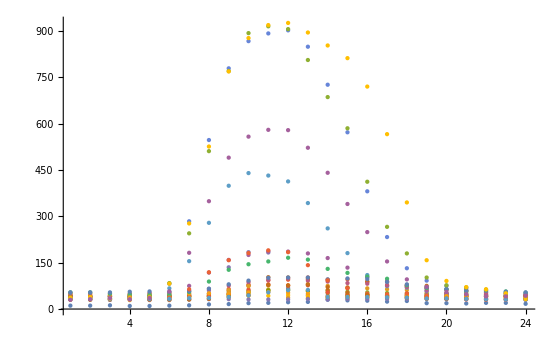

```mathematica
ListPlot[Map[Rest,Select[Select[dataset,MemberQ[specialDays,DateObject[DateList[First[#]][[1;;3]]]]&],Max[Rest[#]]<1000&]],PlotRange->All]
```

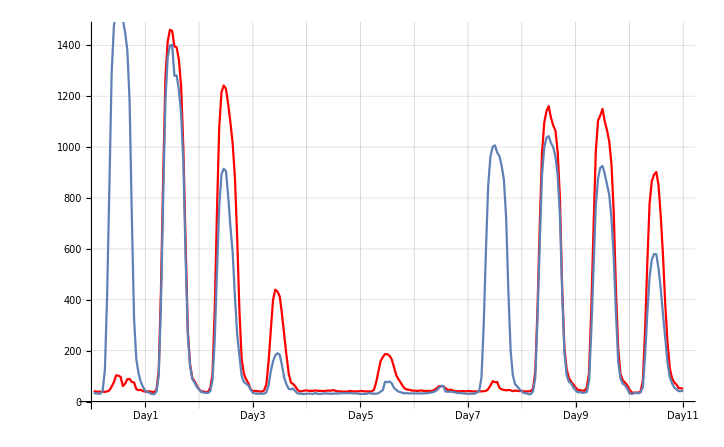

```mathematica
Show[ListLinePlot[Flatten[Map[Rest,Select[dataset,MemberQ[DayRange[DateObject[{2014,12,21}],DateObject[{2014,12,31}]],DateObject[DateList[First[#]][[1;;3]]]]&]]],PlotStyle->Red],ListLinePlot[Flatten[Map[Rest,Select[dataset,MemberQ[DayRange[DateObject[{2015,12,21}],DateObject[{2015,12,31}]],DateObject[DateList[First[#]][[1;;3]]]]&]]]],GridLines->{24*#&/@Range[11],Automatic},Ticks->{{#,"Day"<>ToString[Divide[#,24]]}&/@(24*#&/@Range[11]),Automatic}]
```

```mathematica
(*Above shows the last eleven days, how the occupancies varies. Red is 2014, Blue is 2015*)
```

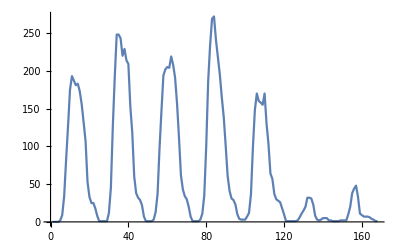

```mathematica
ListLinePlot[Flatten[Map[Rest,dataset[[3;;9]]]]]
```

```mathematica
test1415=Join[Select[dataset,DateValue[First[#],"Year"]==2014&],Select[dataset,DateValue[First[#],"Year"]==2015&]];
```

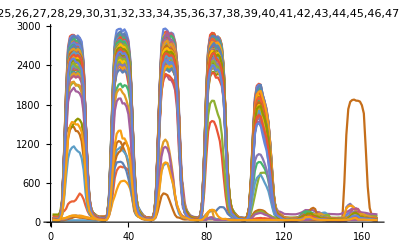

```mathematica
ListLinePlot[Flatten[Join[Map[Rest,test1415][[#;;#+6]]]]&/@Range[6,726,7],PlotLabel->Range[103]]
```

```mathematica
monday=predictDay[Monday]
```

{42.6014,40.2467,38.6764,39.5964,67.9813,245.295,863.315,1650.33,2243.34,2409.03,2468.19,2478.75,2451.5,2456.,2429.22,2347.08,2099.74,1400.36,689.222,288.453,152.952,111.594,86.7198,66.2009}

```mathematica
tuesday=predictDay[Tuesday]
```

{52.7432,47.7677,44.8984,43.5721,73.273,251.045,870.678,1657.04,2272.16,2447.75,2508.36,2508.77,2465.8,2478.36,2439.43,2347.31,2105.45,1401.31,702.019,302.254,164.011,118.786,91.2,68.7135}

```mathematica
wednesday=predictDay[Wednesday]
```

{55.0225,49.8299,47.5483,45.9677,74.5952,252.267,869.095,1668.21,2289.57,2469.7,2536.63,2528.79,2487.55,2491.45,2442.17,2362.31,2108.56,1406.5,711.223,313.527,176.152,127.334,94.6153,71.5393}

```mathematica
thursday=predictDay[Thursday]
```

{57.5435,52.4425,48.6627,48.5259,76.3183,245.345,852.05,1648.84,2255.25,2448.49,2501.76,2503.58,2444.72,2455.84,2416.25,2313.27,2045.08,1351.32,667.111,289.897,162.062,120.27,92.2919,69.3155}

```mathematica
friday=predictDay[Friday]
```

{56.0699,50.7235,48.1831,46.9364,62.3552,154.283,488.59,1021.55,1512.57,1676.98,1719.74,1710.13,1584.12,1486.73,1380.53,1207.36,893.049,534.901,254.479,140.812,100.102,84.931,69.0945,55.6883}

```mathematica
saturday=predictDay[Saturday]
```

{46.689,45.1341,44.7109,44.1976,44.2376,45.2784,49.1641,57.4251,69.7864,83.0623,91.5767,94.6515,94.5986,91.4984,87.5933,80.9096,74.6791,68.4745,62.7671,57.5665,53.3903,51.1566,47.7886,44.6177}

```mathematica
sunday=predictDay[Sunday]
```

{43.6136,42.7831,42.1697,41.6171,41.8632,42.4862,45.6085,52.4075,63.7494,80.913,107.435,115.477,119.294,100.823,85.9059,82.4053,78.1603,72.187,65.3333,60.3364,54.8316,51.1854,48.1912,44.9211}

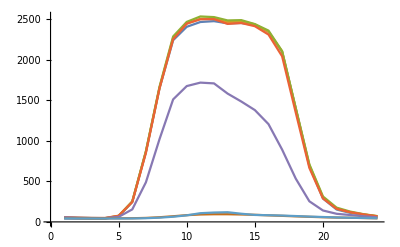

```mathematica
ListLinePlot[{monday,tuesday,wednesday,thursday,friday,saturday,sunday}]
```

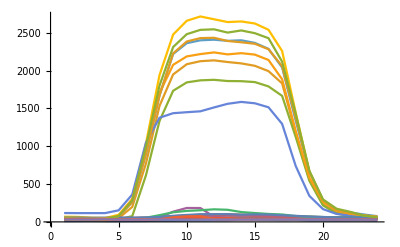

```mathematica
ListLinePlot[Map[Rest,Select[dataset,MemberQ[holidays,DateObject[DateList[First[#]][[1;;3]]]]&]]]
```

```mathematica
Extract[holidays,#]&/@{{#},{#+10}}&/@Range[1,10]
```

{{Wed 1 Jan 2014,Thu 1 Jan 2015},{Mon 20 Jan 2014,Mon 19 Jan 2015},{Mon 17 Feb 2014,Mon 16 Feb 2015},{Mon 26 May 2014,Mon 25 May 2015},{Fri 4 Jul 2014,Fri 3 Jul 2015},{Mon 1 Sep 2014,Mon 7 Sep 2015},{Mon 13 Oct 2014,Mon 12 Oct 2015},{Tue 11 Nov 2014,Wed 11 Nov 2015},{Thu 27 Nov 2014,Thu 26 Nov 2015},{Thu 25 Dec 2014,Fri 25 Dec 2015}}

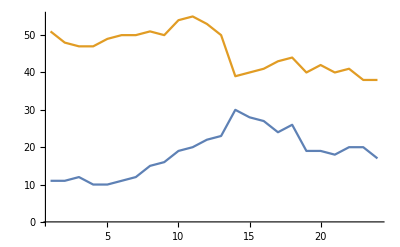
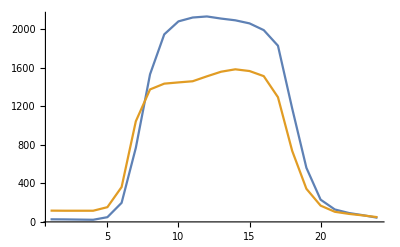
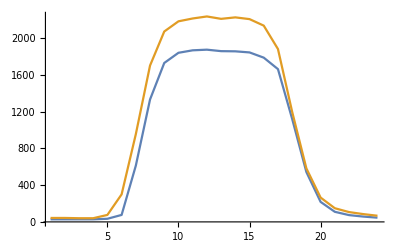
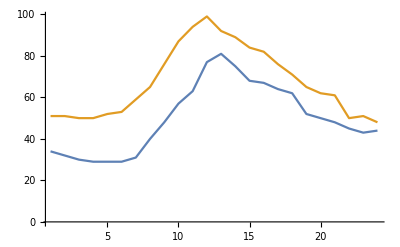
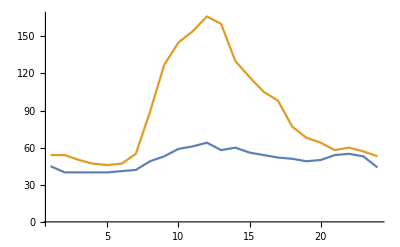
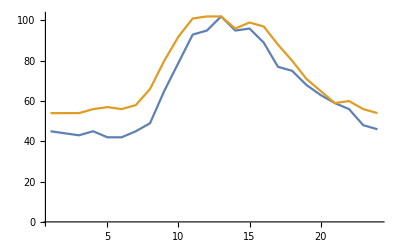
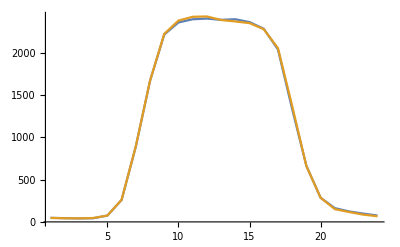
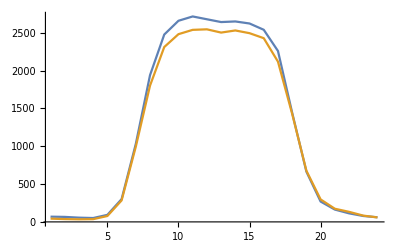

```mathematica
ListLinePlot[Extract[Map[Rest,Select[dataset,MemberQ[holidays,DateObject[DateList[First[#]][[1;;3]]]]&]],{{#},{#+10}}],PlotRange->All]&/@Range[1,10]
```

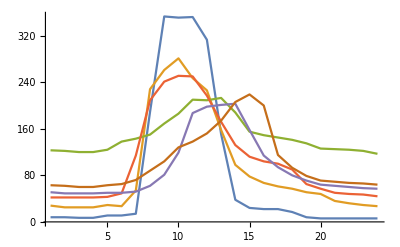

```mathematica
ListLinePlot[Map[Rest,Select[dataset,(DayName[First[#]]==Saturday||DayName[First[#]]==Sunday)&&Max[Rest[#]]>200&]],PlotRange->All]
```

```mathematica
Select[dataset,(DayName[First[#]]==Saturday||DayName[First[#]]==Sunday)&&Max[Rest[#]]>200&]
```

{{2013-02-23 00:00:00,8,8,7,7,11,11,14,189,353,351,352,313,151,38,24,22,22,17,8,6,6,6,6,6},{2014-02-09 00:00:00,28,25,25,25,29,27,54,228,261,281,247,226,158,98,78,67,61,57,51,48,36,32,29,27},{2015-01-18 00:00:00,123,122,120,120,124,138,143,150,169,186,210,209,213,188,155,149,145,141,135,126,125,124,122,117},{2015-02-15 00:00:00,42,42,42,42,43,49,114,209,241,251,250,217,172,132,112,104,100,90,65,57,50,48,47,44},{2015-02-22 00:00:00,51,49,49,49,50,50,52,62,81,119,187,198,201,203,158,114,94,80,71,64,62,60,58,57},{2015-04-11 00:00:00,63,62,60,60,63,65,72,88,104,128,138,152,174,206,219,200,115,93,79,71,69,67,66,64}}

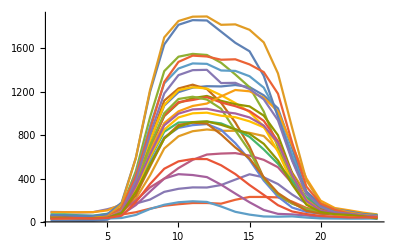

```mathematica
ListLinePlot[Map[Rest,Select[Select[dataset,Max[Rest[#]]<2000&&(DateValue[First[#],"Year"]==2014||DateValue[First[#],"Year"]==2015)&&(DayName[First[#]]==Monday||DayName[First[#]]==Tuesday||DayName[First[#]]==Wednesday||DayName[First[#]]==Thursday)&],FreeQ[holidays,DateObject[DateList[First[#]][[1;;3]]]]&]],PlotRange->All]
```

```mathematica
Select[Select[dataset,Max[Rest[#]]<2000&&(DateValue[First[#],"Year"]==2014||DateValue[First[#],"Year"]==2015)&&(DayName[First[#]]==Monday||DayName[First[#]]==Tuesday||DayName[First[#]]==Wednesday||DayName[First[#]]==Thursday)&],FreeQ[holidays,DateObject[DateList[First[#]][[1;;3]]]]&]//TableForm
```

2014-01-02 00:00:00 | 14 | 14 | 13 | 13 | 20 | 99 | 378 | 743 | 1072 | 1196 | 1238 | 1251 | 1249 | 1262 | 1243 | 1167 | 1047 | 679 | 273 | 119 | 69 | 58 | 48 | 27
2014-01-28 00:00:00 | 48 | 41 | 37 | 34 | 43 | 92 | 214 | 429 | 677 | 789 | 836 | 852 | 840 | 840 | 821 | 792 | 662 | 453 | 263 | 142 | 101 | 77 | 61 | 50
2014-07-03 00:00:00 | 54 | 45 | 43 | 45 | 57 | 134 | 468 | 965 | 1390 | 1523 | 1549 | 1539 | 1467 | 1359 | 1242 | 1018 | 688 | 397 | 195 | 131 | 88 | 81 | 64 | 56
2014-08-07 00:00:00 | 54 | 48 | 43 | 45 | 65 | 68 | 89 | 122 | 149 | 163 | 174 | 174 | 168 | 204 | 230 | 230 | 226 | 187 | 129 | 102 | 79 | 74 | 68 | 54
2014-08-25 00:00:00 | 92 | 90 | 87 | 90 | 117 | 153 | 169 | 206 | 277 | 305 | 318 | 317 | 340 | 390 | 439 | 411 | 349 | 252 | 170 | 115 | 93 | 85 | 74 | 55
2014-11-26 00:00:00 | 45 | 41 | 39 | 38 | 52 | 116 | 398 | 757 | 1118 | 1230 | 1265 | 1225 | 1098 | 917 | 694 | 404 | 234 | 173 | 114 | 92 | 84 | 73 | 56 | 42
2014-12-22 00:00:00 | 40 | 40 | 38 | 37 | 47 | 118 | 439 | 883 | 1277 | 1414 | 1461 | 1457 | 1396 | 1392 | 1343 | 1238 | 993 | 620 | 275 | 145 | 92 | 80 | 63 | 48
2014-12-23 00:00:00 | 40 | 40 | 37 | 38 | 54 | 108 | 364 | 751 | 1079 | 1215 | 1242 | 1229 | 1168 | 1096 | 1013 | 880 | 646 | 359 | 168 | 109 | 87 | 73 | 48 | 41
2014-12-24 00:00:00 | 42 | 41 | 40 | 39 | 44 | 67 | 155 | 279 | 399 | 440 | 432 | 413 | 343 | 261 | 181 | 110 | 74 | 69 | 59 | 45 | 40 | 41 | 43 | 44
2014-12-29 00:00:00 | 40 | 40 | 40 | 41 | 51 | 118 | 364 | 692 | 975 | 1096 | 1141 | 1161 | 1116 | 1085 | 1065 | 980 | 799 | 449 | 208 | 128 | 93 | 78 | 68 | 55
2014-12-30 00:00:00 | 46 | 45 | 43 | 43 | 55 | 113 | 366 | 683 | 982 | 1104 | 1124 | 1150 | 1101 | 1067 | 1022 | 932 | 744 | 436 | 209 | 109 | 84 | 75 | 64 | 48
2014-12-31 00:00:00 | 36 | 35 | 35 | 35 | 40 | 82 | 284 | 547 | 779 | 867 | 892 | 902 | 849 | 726 | 572 | 381 | 233 | 132 | 92 | 75 | 67 | 53 | 52 | 51
2015-04-07 00:00:00 | 88 | 89 | 89 | 90 | 106 | 165 | 397 | 659 | 911 | 1019 | 1069 | 1091 | 1157 | 1216 | 1204 | 1145 | 1018 | 705 | 401 | 196 | 128 | 107 | 85 | 69
2015-05-26 00:00:00 | 48 | 46 | 45 | 45 | 55 | 99 | 197 | 318 | 399 | 496 | 572 | 621 | 630 | 634 | 611 | 572 | 504 | 356 | 217 | 142 | 88 | 66 | 58 | 56
2015-06-16 00:00:00 | 69 | 69 | 61 | 57 | 75 | 111 | 289 | 587 | 831 | 916 | 920 | 925 | 908 | 854 | 784 | 668 | 536 | 376 | 230 | 137 | 106 | 81 | 68 | 64
2015-07-02 00:00:00 | 64 | 60 | 57 | 55 | 71 | 178 | 588 | 1198 | 1636 | 1817 | 1860 | 1857 | 1754 | 1651 | 1573 | 1347 | 968 | 573 | 280 | 160 | 117 | 96 | 73 | 59
2015-11-24 00:00:00 | 40 | 35 | 31 | 35 | 49 | 164 | 589 | 1216 | 1701 | 1852 | 1892 | 1894 | 1817 | 1821 | 1771 | 1655 | 1369 | 865 | 383 | 176 | 118 | 88 | 64 | 53
2015-11-25 00:00:00 | 38 | 33 | 31 | 31 | 42 | 89 | 327 | 698 | 1002 | 1133 | 1154 | 1128 | 1043 | 843 | 653 | 398 | 253 | 168 | 121 | 84 | 74 | 56 | 45 | 37
2015-12-21 00:00:00 | 35 | 32 | 31 | 31 | 44 | 127 | 424 | 850 | 1290 | 1475 | 1533 | 1525 | 1495 | 1499 | 1452 | 1381 | 1182 | 729 | 326 | 167 | 111 | 77 | 57 | 42
2015-12-22 00:00:00 | 37 | 34 | 29 | 29 | 39 | 101 | 382 | 805 | 1184 | 1353 | 1399 | 1402 | 1280 | 1282 | 1225 | 1130 | 937 | 563 | 259 | 139 | 88 | 75 | 57 | 48
2015-12-23 00:00:00 | 37 | 36 | 34 | 34 | 41 | 84 | 245 | 511 | 770 | 893 | 915 | 906 | 806 | 686 | 585 | 412 | 266 | 180 | 102 | 77 | 70 | 63 | 48 | 34
2015-12-24 00:00:00 | 32 | 31 | 31 | 31 | 31 | 36 | 64 | 119 | 158 | 181 | 190 | 184 | 142 | 93 | 67 | 50 | 48 | 51 | 40 | 32 | 31 | 30 | 30 | 31
2015-12-28 00:00:00 | 31 | 31 | 31 | 36 | 42 | 96 | 303 | 597 | 851 | 963 | 1001 | 1007 | 979 | 965 | 927 | 872 | 722 | 432 | 201 | 103 | 68 | 59 | 48 | 40
2015-12-29 00:00:00 | 33 | 33 | 29 | 29 | 40 | 93 | 330 | 623 | 890 | 998 | 1037 | 1043 | 1016 | 1000 | 963 | 888 | 729 | 431 | 194 | 104 | 78 | 72 | 55 | 44
2015-12-30 00:00:00 | 36 | 38 | 34 | 35 | 38 | 82 | 277 | 526 | 769 | 877 | 919 | 926 | 895 | 853 | 812 | 720 | 566 | 345 | 158 | 91 | 71 | 64 | 51 | 32
2015-12-31 00:00:00 | 30 | 32 | 35 | 32 | 36 | 57 | 182 | 349 | 490 | 558 | 580 | 579 | 522 | 441 | 340 | 249 | 154 | 96 | 72 | 55 | 48 | 41 | 41 | 43

```mathematica
Select[Select[dataset,Max[Rest[#]]<1500&&(DateValue[First[#],"Year"]==2014||DateValue[First[#],"Year"]==2015)&&(DayName[First[#]]==Friday)&],FreeQ[holidays,DateObject[DateList[First[#]][[1;;3]]]]&]//TableForm
```

2014-01-03 00:00:00 | 17 | 16 | 14 | 14 | 24 | 73 | 286 | 618 | 988 | 1180 | 1211 | 1211 | 1159 | 1108 | 1041 | 898 | 727 | 475 | 194 | 111 | 73 | 64 | 48 | 27
2014-01-24 00:00:00 | 51 | 45 | 43 | 43 | 50 | 72 | 142 | 269 | 408 | 556 | 679 | 754 | 756 | 759 | 739 | 677 | 553 | 383 | 206 | 105 | 71 | 63 | 42 | 32
2014-04-18 00:00:00 | 44 | 37 | 38 | 37 | 43 | 89 | 263 | 530 | 785 | 897 | 921 | 918 | 872 | 821 | 751 | 627 | 449 | 258 | 137 | 83 | 63 | 56 | 38 | 32
2014-11-28 00:00:00 | 43 | 43 | 42 | 42 | 44 | 47 | 62 | 96 | 153 | 170 | 177 | 175 | 162 | 148 | 130 | 114 | 99 | 79 | 68 | 62 | 56 | 47 | 43 | 45
2014-12-26 00:00:00 | 41 | 40 | 40 | 40 | 40 | 46 | 75 | 118 | 159 | 175 | 187 | 186 | 180 | 165 | 134 | 103 | 87 | 74 | 59 | 50 | 47 | 46 | 43 | 43
2015-01-02 00:00:00 | 38 | 38 | 38 | 37 | 41 | 73 | 219 | 427 | 594 | 674 | 708 | 724 | 671 | 606 | 547 | 472 | 349 | 221 | 116 | 79 | 64 | 48 | 42 | 41
2015-04-03 00:00:00 | 69 | 62 | 60 | 60 | 71 | 138 | 347 | 681 | 936 | 1017 | 1041 | 1033 | 976 | 900 | 804 | 665 | 432 | 297 | 190 | 155 | 118 | 86 | 76 | 63
2015-11-27 00:00:00 | 33 | 33 | 33 | 33 | 35 | 35 | 52 | 83 | 117 | 127 | 136 | 140 | 132 | 116 | 107 | 95 | 73 | 64 | 48 | 35 | 33 | 33 | 33 | 33

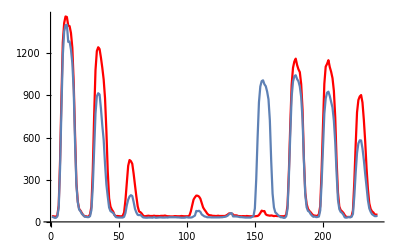

```mathematica
Show[ListLinePlot[Flatten[Join[Map[Rest,Take[Select[dataset,DateValue[First[#],"Year"]==2014&],-10]]]],PlotStyle->Red],ListLinePlot[Flatten[Join[Map[Rest,Take[Select[dataset,DateValue[First[#],"Year"]==2015&],-10]]]]]]
```

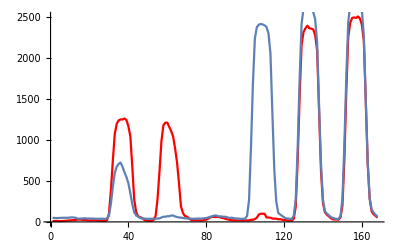

```mathematica
Show[ListLinePlot[Flatten[Join[Map[Rest,Take[Select[dataset,DateValue[First[#],"Year"]==2014&],7]]]],PlotStyle->Red],ListLinePlot[Flatten[Join[Map[Rest,Take[Select[dataset,DateValue[First[#],"Year"]==2015&],7]]]]]]
```

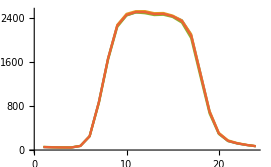

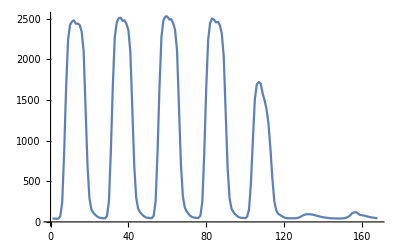

```mathematica
ListLinePlot[{tuesday,wednesday,thursday,Mean[{tuesday,wednesday,thursday}]}]
```

```mathematica
func[l_List]:=MapAt[#+120&,l,Position[l,_?(#>2000&)]]
```

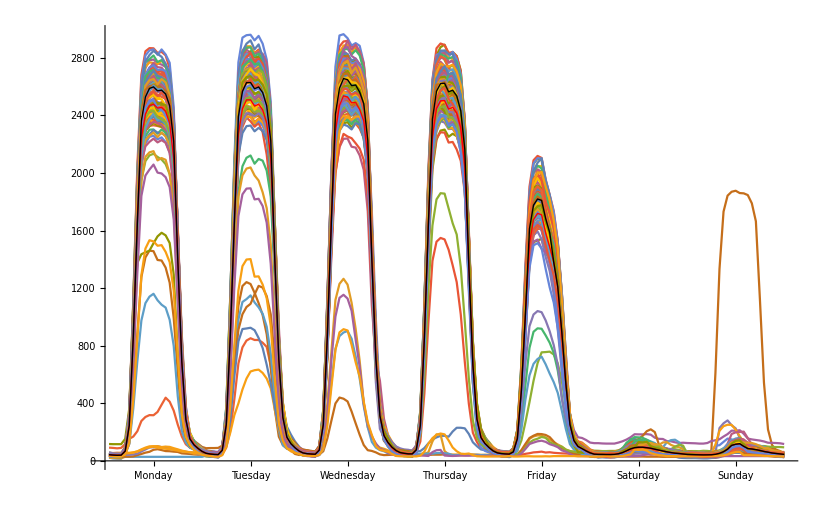

```mathematica
Show[ListLinePlot[Flatten[Join[Map[Rest,test1415][[#;;#+6]]]]&/@Range[6,726,7]],ListLinePlot[Join[monday,tuesday,wednesday,thursday,friday,saturday,sunday],PlotStyle->{Red,Thick}],ListLinePlot[Flatten[Join[func[#]&/@{monday,tuesday,wednesday,thursday},MapAt[#+100&,friday,Position[friday,_?(#>1450&)]],saturday,sunday]],PlotStyle->{Black,Thick}],Ticks->{{{12,"Monday"},{36,"Tuesday"},{60,"Wednesday"},{84,"Thursday"},{108,"Friday"},{132,"Saturday"},{156,"Sunday"}},Automatic}]
```

```mathematica
Transpose[Map[Round,Join[func[#]&/@{monday,tuesday,wednesday,thursday},{MapAt[#+100&,friday,Position[friday,_?(#>1450&)]]},{saturday,sunday}]]]//TableForm
```

43 | 53 | 55 | 58 | 56 | 47 | 44
40 | 48 | 50 | 52 | 51 | 45 | 43
39 | 45 | 48 | 49 | 48 | 45 | 42
40 | 44 | 46 | 49 | 47 | 44 | 42
68 | 73 | 75 | 76 | 62 | 44 | 42
245 | 251 | 252 | 245 | 154 | 45 | 42
863 | 871 | 869 | 852 | 489 | 49 | 46
1650 | 1657 | 1668 | 1649 | 1022 | 57 | 52
2363 | 2392 | 2410 | 2375 | 1613 | 70 | 64
2529 | 2568 | 2590 | 2568 | 1777 | 83 | 81
2588 | 2628 | 2657 | 2622 | 1820 | 92 | 107
2599 | 2629 | 2649 | 2624 | 1810 | 95 | 115
2571 | 2586 | 2608 | 2565 | 1684 | 95 | 119
2576 | 2598 | 2611 | 2576 | 1587 | 91 | 101
2549 | 2559 | 2562 | 2536 | 1381 | 88 | 86
2467 | 2467 | 2482 | 2433 | 1207 | 81 | 82
2220 | 2225 | 2229 | 2165 | 893 | 75 | 78
1400 | 1401 | 1407 | 1351 | 535 | 68 | 72
689 | 702 | 711 | 667 | 254 | 63 | 65
288 | 302 | 314 | 290 | 141 | 58 | 60
153 | 164 | 176 | 162 | 100 | 53 | 55
112 | 119 | 127 | 120 | 85 | 51 | 51
87 | 91 | 95 | 92 | 69 | 48 | 48
66 | 69 | 72 | 69 | 56 | 45 | 45

```mathematica
Export["test.csv",Transpose[Map[Round,Join[func[#]&/@{monday,tuesday,wednesday,thursday},{MapAt[#+100&,friday,Position[friday,_?(#>1450&)]]},{saturday,sunday}]]]]
```

test.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["test.csv"]]]
```

```mathematica
Position[monday,_?(#>2000&)]
```

{{9},{10},{11},{12},{13},{14},{15},{16},{17}}

```mathematica
friday
```

{56.0794,50.5682,48.1528,46.6311,62.4417,153.934,490.278,1019.54,1512.38,1691.74,1721.82,1702.09,1580.89,1495.14,1385.97,1210.25,898.238,532.307,254.636,141.327,99.0488,84.7984,68.6087,55.314}

```mathematica
Position[friday,_?(#>1400&)]
```

{{9},{10},{11},{12},{13},{14}}